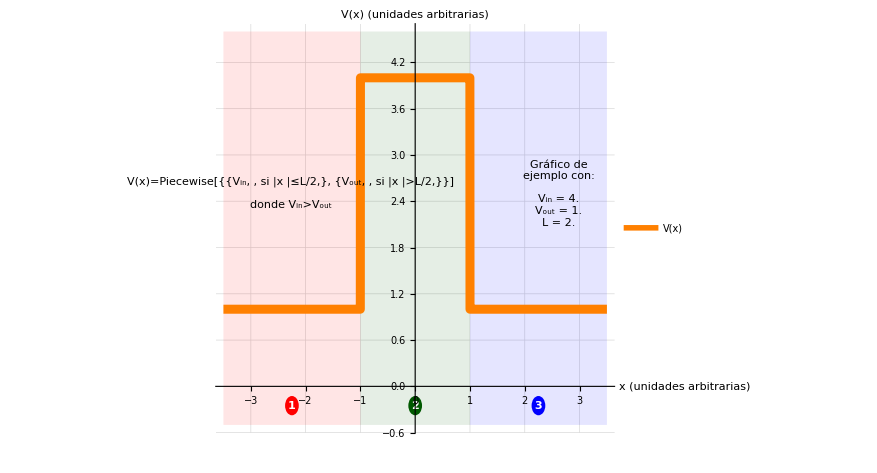
Barrera de potencial.

Una barrera de potencial difiere del pozo en que  V_in>V_out. 

-Graphics-


La teoría general para una barrera de potencial finita tiene muchas similitudes con el pozo de potencial, pues la función de onda también se debe construir como una función con 3 tramos en cuyos límites se impone continuidad de la función de onda y de sus derivadas: 
	•  ESIT: -ℏ^2/(2m)(ⅆ^2 ψ_j)/(ⅆ x^2)+V_j ψ_j= ℰ ψ_j, 	donde 	j=1,2,3, 	V_1=V_3=V_out 	y	V_2=V_in. 
	•  La ESIT es equivalente a ψ''_j(x)+k_j^2 ψ_j(x)=0, donde k_j=√((2m)/ℏ^2(ℰ-V_j)).
	• Soluciones ψ_j(x)=A_j ⅇ^(ⅈ k_j x)+B_j ⅇ^(-ⅈ k_j x), donde los A_j y B_j son incógnitas. 
	• Para resolver los coeficientes, imponemos continidad de ψ(x) y ψ'(x) para x=-L/2 y para x=+L/2.
	• Parámetros auxiliares similares a los del pozo finito, con algunas diferencia:
			◦ ΔV=V_in-V_out se definirá como la “altura” de la barrera.
			◦ Δℰ=ℰ-V_out será cuánto sobresale la energía respecto del mínimo (afuera) del potencial.
	• Reutilizamos las definiciones η | = | Δℰ/ΔV,  λ_dB | = | √((2 π^2 ℏ^2)/(m Δℰ)) y Λ | = | L/λ_dB.
	• Como consecuencia de las nuevas definiciones, 
			◦ k_in cambia a k_in | = | √((2m)/ℏ^2 Δℰ) | = | √((2m ΔV)/ℏ^2)√(η-1).
			◦ k_out cambia a k_out | = | √((2m)/ℏ^2(Δℰ-ΔV)) | = | √((2m ΔV)/ℏ^2)√η.
			◦ Se mantiene Λ | = | L √(m/(2 π^2 ℏ^2)Δℰ) | = | L/(2π)√((2m ΔV)/ℏ^2)√η.

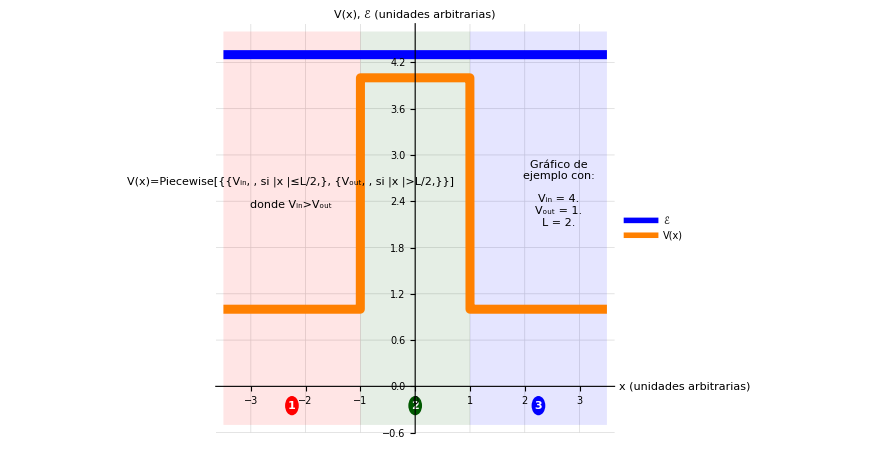
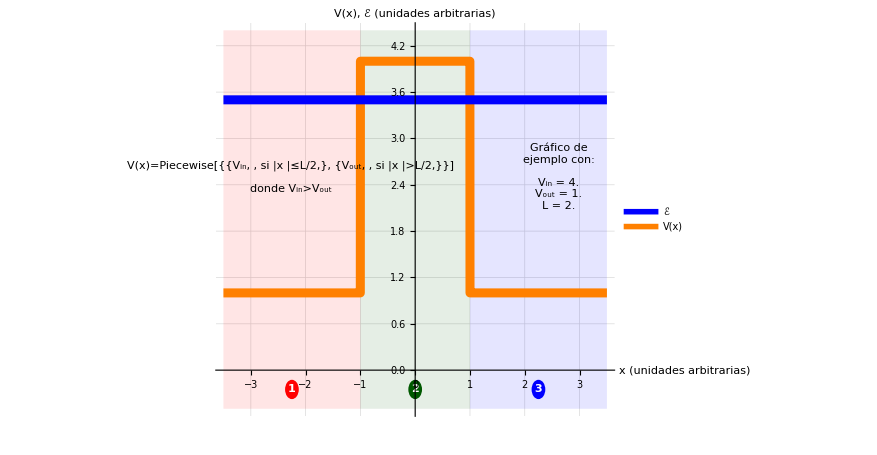
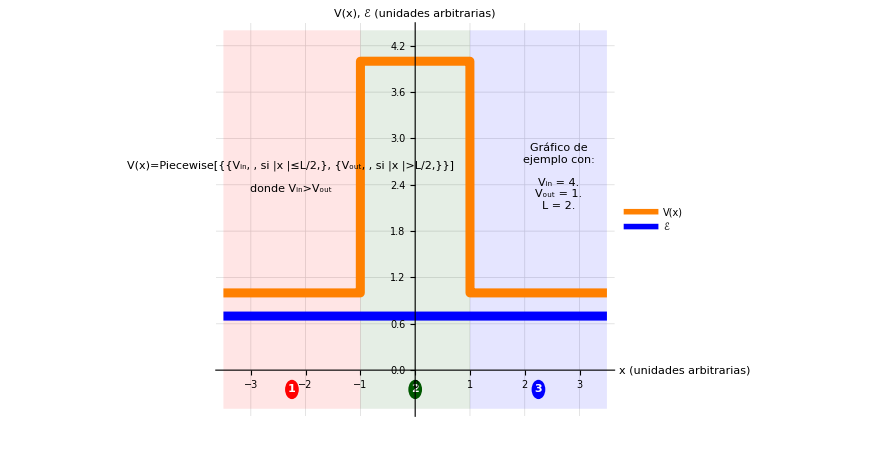
Caso (a): ℰ>V_in>V_out

-Graphics-
Todos los k_j son reales y positivos, de modo que las soluciones son oscilatorias en las tres regiones. Nuevamente, supondremos que la onda viene desde la izquierda, de modo que A_1 será usado como coeficiente de referencia. No habiendo con qué reflejarse en la Región 3, podemos ya considerar que B_3=0. Este caso será estudiado en función de que η>1.


Caso (b): V_in>ℰ>V_out

-Graphics-
Ocurrirá que k_out  es real y positivo, mientras que k_in=ⅈγ_in será un imaginario puro. Es decir, las eigenfunciones serán oscilatorias fuera de la barrera y exponenciales dentro de ella. Al igual que en los otros casos analizados, supondremos que (i) la onda viene desde la izquierda para usar A_1 como coeficiente de referencia y (ii) no hay nada con qué reflejarse en la Región 3, de modo que B_3=0.

No obstante, a diferencia del pozo finito, el comportamiento exponencial en la Región 2 no permite anular alguna de las incógnitas. Esto se debe a que ninguna de las exponenciales diverge allí, pues es una región espacialmente acotada sin que ocurra │x│→∞.  

De este modo, este caso no es matemáticamente tan distinto al caso (a), salvo por 0<η≤1, de modo que los estudiaremos juntos. 


Caso (c): V_in>V_out>ℰ

-Graphics-
Al igual como ocurrió con el pozo de potencial, este caso solo conduce a que ψ(x)=0. Es decir, la partícula no puede existir en un estado cuya energía esté por debajo del mínimo absoluto del potencial. Debido a aquello, solo estudiaremos los casos (a) y (b). 


¿Cómo unificamos los casos (a) y (b)?

Ambos tienen un k_out real y positivo, de modo que la naturaleza de las funciones será la misma afuera de la barrera. La única diferencia estará dentro del la barrera. 
	• 	Si Δℰ>ΔV, tendremos que η>1, k_in>0 y k_in^2>0. 
		La onda se moverá como (Onda oscilatoria)_(Región 1,  ⇌)→(Onda oscilatoria)_(Región 2,  ⇌)→(Onda oscilatoria)_(Región 3,  →).

	• 	Si Δℰ<ΔV, tendremos que 0<η≤1, k_in=ⅈγ_in y k_in^2≤0. 
		La onda se moverá como (Onda oscilatoria)_(Región 1,  ⇌)→(Onda evanescente)_(Región 2,  ⇌)→(Onda oscilatoria)_(Región 3,  →).

Ambos casos tendrán 5 términos, respectivamente asociados a A_1, B_1, A_2, B_2 y A_3. Y ambos casos constituirán sistemas de 4 ecuaciones para 5 coeficientes. Si ocupamos A_1 como referencia, estas 4 ecuaciones pasan a ser un sistema inhomogéneo para B_1, A_2, B_2 y A_3. No será necesario imponer condiciones adicionales de dependencia lineal y, en consecuencia, no aparece discretización en la energía. 

En términos de cálculo, se tratará de permitir valores imaginarios para k_in. El recordar que cos(ⅈx)=cosh(x) y sin(ⅈx)=ⅈsinh(x) ayudará a unificar las expresiones, que ahora se tratarán únicamente en términos de 0<η<∞, en lugar de separarlo en dos casos. 


Sistema de ecuaciones y coeficientes de reflexión y transmisión.

Si representamos matricialmente el sistema de ecuaciones debido a las condiciones de continuidad, tendremos

	(ⅇ^(1/2 ⅈ L k_out) | -ⅇ^(-1/2 ⅈ L k_in) | -ⅇ^(1/2 ⅈ L k_in) | 0
-ⅈ k_out ⅇ^(1/2 ⅈ L k_out) | -ⅈ k_in ⅇ^(-1/2 ⅈ L k_in) | ⅈ k_in ⅇ^(1/2 ⅈ L k_in) | 0
0 | ⅇ^(1/2 ⅈ L k_in) | ⅇ^(-1/2 ⅈ L k_in) | -ⅇ^(1/2 ⅈ L k_out)
0 | ⅈ k_in ⅇ^(1/2 ⅈ L k_in) | -ⅈ k_in ⅇ^(-1/2 ⅈ L k_in) | -ⅈ k_out ⅇ^(1/2 ⅈ L k_out))·(B_1
A_2
B_2
A_3)==-A_1(ⅇ^(-1/2 ⅈ L k_out)
ⅈ k_out ⅇ^(-1/2 ⅈ L k_out)
0
0) 


Al igual que con el caso (a) del pozo de potencial, podemos definir amplitudes de reflexión (𝓇) y transmisión (𝓉), que contienen información de con cuánta probabilidad ocurrirá cada opción y si la onda gana alguna fase en ellas. 

	𝓇=B_1/A_1 	y 	𝓉=A_3/A_1.

Nuevamente, las probabilidades de que la partícula termine siendo reflejada o transmitida son los cocientes entre la corriente de probabilidad reflejada (o transmitida) y la incidente. 

	R | = | (│𝓇│)^2 | = | (2 (k_in^2-k_out^2)^2 sin^2(L k_in))/(6 k_in^2 k_out^2+k_in^4+k_out^4 - (k_in^2-k_out^2)^2 cos(2 L k_in)) 	 y 	T | = | (│𝓉│)^2 | (8 k_in^2 k_out^2)/(6 k_in^2 k_out^2+k_in^4+k_out^4 - (k_in^2-k_out^2)^2 cos(2 L k_in))  

La parte potencialmente oscilatoria de estas probabilidades están en las funciones trigonométricas cos(2 L k_in) y sin^2(L k_in). 
	◦ Si la energía de la partícula es mayor que la altura máxima de la barrera (η>1), ocurrirá que R y T exhibirán máximos y mínimos para diversos valores de L. Aparecerán resonancias (máximos en la transmisión o en la reflexión) y “anti-resonancias”.
	◦ Si la energía de la partícula no supera el máximo de la barrera (0<η≤1), estas funciones oscilatorias se transforman en funciones hiperbólicas. 

* Para ver los gráficos interactivos, ejecute la siguiente celda y vaya al final del archivo.

```mathematica
Remove["Global`*"];
$Assumptions=And@@Thread[{Subscript[k, out],Subscript[Κ, P],Subscript[γ, in],Subscript[γ, out],L,ℒ,Λ,Subscript[λ, P],Subscript[λ, dB],m,ℏ,ℰ,η,Subscript[V, in],Subscript[V, out],ΔV,Δ𝒱,𝒜^◦,𝓂,𝓈,ℯ𝒱}>0]&&Δℰ>0&&Subscript[k, in]∈Reals;

(* Funciones de onda posibles. *)
Subscript[ψ, j_][x_]:=Subscript[A, j] ⅇ^(ⅈ Subscript[κ, j] x)+Subscript[B, j] ⅇ^(-ⅈ Subscript[κ, j] x);


(* Reducción de parámetros. *)
(* ΔV = Subscript[V, out] - Subscript[V, in], "profundidad" del pozo. *)
Reduccion={
	Subscript[k, in]->√((2m)/ℏ^2(ℰ-Subscript[V, in])),
	Subscript[k, out]->√((2m)/ℏ^2(ℰ-Subscript[V, out])),
	ℰ->Δℰ+Subscript[V, out],
	Subscript[V, in]->ΔV+Subscript[V, out],
	Δℰ->η ΔV,
	Subscript[λ, dB]->√((2 π^2 ℏ^2)/(m Δℰ)),
	L->Λ Subscript[λ, dB]		
};


(*"
Para gráficos, consideremos un electrón en un pozo que tiene unos cuantos årmströng de ancho y unos cuantos electronvolts de profundidad. Podemos ir cambiando L y ΔV.
"*)
Numeros={
		Subscript[k, in]->√((2m)/ℏ^2(ℰ-Subscript[V, in])),
		Subscript[k, out]->√((2m)/ℏ^2(ℰ-Subscript[V, out])),
		Subscript[λ, dB]->√((2 π^2 ℏ^2)/(m Δℰ)),
		ℰ->Δℰ+Subscript[V, out],
		Subscript[V, in]->ΔV+Subscript[V, out],
		Δℰ->η ΔV,
		c->299792458 𝓂/𝓈,
		ℏ->6.62607015/(2π)×10^-34 𝒥 𝓈,
		𝒥->ℯ𝒱/(1.60217663×10^-19),
		m->0.511 ×10^6 ℯ𝒱/c^2,
		𝓂->𝒜^◦/10^-10,
		L->ℒ 𝒜^◦,                                       (* ℒ: Ancho del pozo, pero medido en årmströngs. *)
		ΔV->Δ𝒱 ℯ𝒱,		             (* Δ𝒱: profundidad del pozo, pero medido en electronvolts. *)
		σ->5                                       (* σ: ancho del paquete de onda, en årmströngs. *)
};

(* Funciones solo para ayudar en la presentación de resultados. *)
TsT[args__]:=TraditionalForm[StringRiffle[ToString[#,TraditionalForm]&/@{args}]]

(* Condiciones de continuidad. *)
Continuidad={
			Subscript[ψ, 1][-L/2]==Subscript[ψ, 2][-L/2],
			Subscript[ψ, 1]'[-L/2]==Subscript[ψ, 2]'[-L/2],
			Subscript[ψ, 2][L/2]==Subscript[ψ, 3][L/2],
			Subscript[ψ, 2]'[L/2]==Subscript[ψ, 3]'[L/2]
			};


SubsAB={Subscript[κ, 1]->Subscript[k, out],Subscript[κ, 2]->Subscript[k, in],Subscript[κ, 3]->Subscript[k, out],Subscript[B, 3]->0};
Subscript[Eqs, ab]=Continuidad//.SubsAB;
Subscript[v, ab]={Subscript[B, 1],Subscript[A, 2],Subscript[B, 2],Subscript[A, 3]};

(* Podemos expresar el sistema de ecuaciones como M·v⃗=b⃗, donde: *)
{Subscript[b, ab],Subscript[M, ab]}=Normal[CoefficientArrays[Subscript[Eqs, ab],Subscript[v, ab]]];
Subscript[b, ab]=-Subscript[b, ab];             (* CoefficientArrays construye como Subscript[M, a].Subscript[v, a]+Subscript[b, a]=0. Nosotros usamos Subscript[M, a].Subscript[v, a]=Subscript[b, a]. *)

(* El sistema es inhomogéneo y se puede resolver sin caer en la solución trivial. *)
Subscript[S, ab]=Flatten[FullSimplify[Solve[Subscript[Eqs, ab],Subscript[v, ab]]]];


TsT["\nSistema matricial M·v⃗ = b⃗\n",
	Subscript[M, ab]·{Subscript[v, ab]}ᵀ=={Subscript[b, ab]}ᵀ,"\n\nSoluciones:\n",Flatten["\n"Subscript[S, ab]]]

(* Nos interesan los coeficientes de reflexión y transmisión. *)
𝓇𝓉=FullSimplify[{Subscript[B, 1]/Subscript[A, 1],Subscript[A, 3]/Subscript[A, 1]}//. Subscript[S, ab]];
RT=FullSimplify[𝓇𝓉* * 𝓇𝓉];
TsT["Cell["𝓇 = ",ExpressionUUID->"fc38d7ab-31da-46f6-a61c-8ac46b3ae33f"]",𝓇𝓉⟦1⟧,"\n","Cell["𝓉 =",ExpressionUUID->"8cf61fc4-142b-4d94-8f57-f4e5da94561f"]",𝓇𝓉⟦2⟧,"\n","R = |𝓇|^2 = ",RT⟦1⟧,"\n","T = |𝓉|^2 = ",RT⟦2⟧]



(*" 
Grafiquemos estos coeficientes en función de la energía y la longitud, pero usando los parámetros reducidos. Es decir, energía como múltiplo de la profundidad del pozo y ancho del pozo como múltiplos de la longitud de onda de de Broglie. 
"*)
ηmin=0.01;
ηmax=3.0;
Λmin=0.01;
Λmax=6.0;
{dbR[η_,Λ_],dbT[η_,Λ_]}=FullSimplify[RT//.Reduccion];
TsT["Si Λ = L/λ_dB, entonces Cell["R = ",ExpressionUUID->"c9e5608c-ed60-4daa-96f4-d0011d31c2c0"]",dbR[η,Λ],"\t y \t","Cell["T = ",ExpressionUUID->"5000ad47-f5a5-477e-b369-2289696b26ba"]",dbT[η,Λ],"."]
Manipulate[
		Plot[{dbR[η,Λ],dbT[η,Λ]},
			{Λ,Λmin,Λmax},
			PlotPoints->Ceiling[30(Λmax-Λmin)],
			PlotLegends->{"R","T"},
			AxesLabel->{"Λ = L/λ_dB","R, T"},
			PlotLabel->("Coeficientes de reflexión y transmisión\n"
						<>"Δℰ = "<>ToString[η]<>" ΔV"),
			GridLines->Automatic],
		{{η,1.02},ηmin,ηmax,(ηmax-ηmin)/100.},
		LabelStyle->Large,
		ControlPlacement->Top,
		SynchronousUpdating->False]



(*"
Más ejemplos gráficos, con números variados. 
Longitudes en amstrongs, energías en electronvolts. 
"*)
ℒmin=1.;
ℒmax=30.;
ΔVmin=1.;
ΔVmax=20.;
{B1[η_,ℒ_,Δ𝒱_],
A2[η_,ℒ_,Δ𝒱_],
B2[η_,ℒ_,Δ𝒱_],
A3[η_,ℒ_,Δ𝒱_]}=N[FullSimplify[{Subscript[B, 1],Subscript[A, 2],Subscript[B, 2],Subscript[A, 3]}//. Subscript[S, ab]//.Numeros//.{Subscript[A, 1]->1}]];
numKin[η_,Δ𝒱_]=N[FullSimplify[Subscript[k, in] × 𝒜^◦//.Numeros]];
numKout[η_,Δ𝒱_]=N[FullSimplify[Subscript[k, out]× 𝒜^◦//.Numeros]];
A1=0.05ΔVmax ηmax;
KinMax=numKin[ηmax,ΔVmax];
dxmin=(2π)/(16KinMax);

colores=ColorData[97]/@Range[100];
colores[[7,All]]={0,0,0};
leyenda=LineLegend[colores,
				{"Incidente desde 1",
				"Reflejado en frontera 1|2",
				"Transmitido 1→2",
				"Reflejado en frontera 2|3",
				"Transmitido 2→3",
				"Potencial",
				"Re[ψ(x)]"},
				LabelStyle->Larger];
Manipulate[
		kout=numKout[η,Δ𝒱]; 
		kin=numKin[η,Δ𝒱];
		B1n=B1[η,ℒ,Δ𝒱];
		A2n=A2[η,ℒ,Δ𝒱];
		B2n=B2[η,ℒ,Δ𝒱];
		A3n=A3[η,ℒ,Δ𝒱];
		h0=η Δ𝒱;
		LdB=ℒ/(2π/kin);

		xMax=(ℒmax+5.ℒ)/6.0;
		
		npin=Ceiling[ℒ/dxmin];
		npout=Ceiling[(xMax-ℒ/2)/dxmin];
		𝓍1=Subdivide[-xMax,-ℒ/2,npout];
		𝓍2=Subdivide[-ℒ/2,ℒ/2,npin];
		𝓍3=Subdivide[ℒ/2,xMax,npout];
		sfactor=1.05;
		ymaxW=sfactor Piecewise[{{η Δ𝒱, η>1}, {Δ𝒱, η<=1}}];

		zz={B1n,A2n,B2n,A3n};
		A0=(sfactor-1)/sfactor ymaxW;
		A1=Min[Abs[A0/zz]];
		
		W1d=Exp[+ ⅈ kout 𝓍1];
		W1i=Exp[- ⅈ kout 𝓍1]×B1n;
		W2d=Exp[+ ⅈ kin 𝓍2  ]×A2n;
		W2i=Exp[- ⅈ kin 𝓍2  ]×B2n;
		W3d=Exp[+ ⅈ kout 𝓍3]×A3n;

		Onda1d=h0+A1 Re[W1d];
		Onda1i=h0+A1 Re[W1i];
		Onda2d=h0+A1 Re[W2d];
		Onda2i=h0+A1 Re[W2i];
		Onda3d=h0+A1 Re[W3d];
		Onda123=h0+A1 Re[Flatten[{W1d+W1i,W2d+W2i,W3d}]];
		𝓍123=Flatten[{𝓍1,𝓍2,𝓍3}];
		Vx={{-ℒmax,0},{-ℒ/2,0},{-ℒ/2,Δ𝒱},{ℒ/2,Δ𝒱},{ℒ/2,0},{ℒmax,0}};
		
		
		
					
		PlotW=ListLinePlot[
					{{𝓍1,Onda1d}ᵀ,
					{𝓍1,Onda1i}ᵀ,
					{𝓍2,Onda2d}ᵀ,
					{𝓍2,Onda2i}ᵀ,
					{𝓍3,Onda3d}ᵀ,
					Vx,
					{𝓍123,Onda123}ᵀ},
					PlotStyle->colores,
					PlotLabel->("Δℰ = "<>ToString[η]<>" ΔV,\t"<>
							"ΔV = "<>ToString[Δ𝒱]<>" eV,\r"<>
							"L = "<>ToString[ℒ]<>" Å \t (o "<>ToString[LdB]<>"λ_dB),\r\r"<>
							"R = "<>ToString[TraditionalForm[Abs[B1n]^2]]<>",\t"<>
							"T = "<>ToString[TraditionalForm[Abs[A3n]^2]]<>"."),
					GridLines->{{-ℒ/2,ℒ/2},{}},
					PlotRange->{{-1,1}xMax,{-0.01ΔVmax,ymaxW}},
					FrameLabel->{"x, en Å","V(x), ψ(x)"},
					Frame->True];
		pos=Last@Position[PlotW,_Line];
		PlotW2=MapAt[{Thickness[0.003],Dashed,#}&,PlotW,pos];
		Legended[PlotW2,Placed[leyenda,Right]],
		{{η,(ηmax+ηmin)/2.0},ηmin,ηmax,((ηmax-ηmin)/100.0)},
		{{ℒ,(ℒmax+ℒmin)/2.0},ℒmin,ℒmax,((ℒmax-ℒmin)/100.0)},
		{{Δ𝒱,(ΔVmax+ΔVmin)/2.0},ΔVmin,ΔVmax,((ΔVmax-ΔVmin)/100.0)},
		LabelStyle->Larger,
		ControlPlacement->Top,
		SynchronousUpdating->False]
```

Sistema matricial M·v⃗ = b⃗
 (ⅇ^(1/2 ⅈ L k_out) | -ⅇ^(-1/2 ⅈ L k_in) | -ⅇ^(1/2 ⅈ L k_in) | 0
-ⅈ k_out ⅇ^(1/2 ⅈ L k_out) | -ⅈ k_in ⅇ^(-1/2 ⅈ L k_in) | ⅈ k_in ⅇ^(1/2 ⅈ L k_in) | 0
0 | ⅇ^(1/2 ⅈ L k_in) | ⅇ^(-1/2 ⅈ L k_in) | -ⅇ^(1/2 ⅈ L k_out)
0 | ⅈ k_in ⅇ^(1/2 ⅈ L k_in) | -ⅈ k_in ⅇ^(-1/2 ⅈ L k_in) | -ⅈ k_out ⅇ^(1/2 ⅈ L k_out))·(B_1
A_2
B_2
A_3)==(A_1 (-ⅇ^(-1/2 ⅈ L k_out))
-ⅈ A_1 k_out ⅇ^(-1/2 ⅈ L k_out)
0
0) 

Soluciones:
 {
 (B_1→(A_1 (-1+ⅇ^(2 ⅈ L k_in)) (k_out^2-k_in^2) ⅇ^(-ⅈ L k_out))/(-(k_in+k_out)^2+ⅇ^(2 ⅈ L k_in) (k_in-k_out)^2)),
 (A_2→-(2 A_1 k_out (k_in+k_out) ⅇ^(1/2 ⅈ L (k_in-k_out)))/(-(k_in+k_out)^2+ⅇ^(2 ⅈ L k_in) (k_in-k_out)^2)),
 (B_2→-(2 A_1 k_out (k_in-k_out) ⅇ^(1/2 ⅈ L (3 k_in-k_out)))/(-(k_in+k_out)^2+ⅇ^(2 ⅈ L k_in) (k_in-k_out)^2)),
 (A_3→-(4 A_1 k_in k_out ⅇ^(ⅈ L (k_in-k_out)))/(-(k_in+k_out)^2+ⅇ^(2 ⅈ L k_in) (k_in-k_out)^2))}

Cell["𝓇 = "] ((-1+ⅇ^(2 ⅈ L k_in)) (k_out^2-k_in^2) ⅇ^(-ⅈ L k_out))/(-(k_in+k_out)^2+ⅇ^(2 ⅈ L k_in) (k_in-k_out)^2) 
 Cell["𝓉 ="] -(4 k_in k_out ⅇ^(ⅈ L (k_in-k_out)))/(-(k_in+k_out)^2+ⅇ^(2 ⅈ L k_in) (k_in-k_out)^2) 
 R = |𝓇|^2 =  (2 (k_in^2-k_out^2)^2 sin^2(L k_in))/(-(k_in^2-k_out^2)^2 cos(2 L k_in)+6 k_in^2 k_out^2+k_in^4+k_out^4) 
 T = |𝓉|^2 =  (8 k_in^2 k_out^2)/(-(k_in^2-k_out^2)^2 cos(2 L k_in)+6 k_in^2 k_out^2+k_in^4+k_out^4)

Si Λ = L/λ_dB, entonces Cell["R = "] (2 sin^2(2 π √((η-1)/η) Λ))/(-cos(4 π √((η-1)/η) Λ)+8 (η-1) η+1) 	 y 	 Cell["T = "] (8 (η-1) η)/(-cos(4 π √((η-1)/η) Λ)+8 (η-1) η+1) .